n = 7

Таблица данной функции:
XDT:   (-π
-(5 π)/7
-(3 π)/7
-π/7
π/7
(3 π)/7
(5 π)/7
π)    YDT:    (3.14159
1.39911
-0.299601
-0.404354
0.404354
0.299601
-1.39911
-3.14159)

Вычисляем таблицу разностей по рекуррентной формуле:

3.1415926540 | -1.9412754950 |  0.0271667245 |  0.3572611568 | -0.1431852795 |  0.0155074686 |  0.0032096406 | -0.0010216603
 1.3991078440 | -1.8925059060 |  0.9891973179 | -0.1568300684 | -0.0735879231 |  0.0327932688 | -0.0032096406 | 
-0.2996014849 | -0.1167030330 |  0.5668862972 | -0.4210395297 |  0.0735879231 |  0.0155074686 |  | 
-0.4043538824 |  0.9009688679 | -0.5668862972 | -0.1568300684 |  0.1431852795 |  |  | 
 0.4043538824 | -0.1167030330 | -0.9891973179 |  0.3572611568 |  |  |  | 
 0.2996014849 | -1.8925059060 | -0.0271667245 |  |  |  |  | 
-1.3991078440 | -1.9412754950 |  |  |  |  |  | 
-3.1415926540 |  |  |  |  |  |  |

Интреполяционные многочлены 1, 2, 3, 4 порядка:

3.14159-1.94128 (π+x)
3.14159-1.94128 (π+x)+0.0271667 ((5 π)/7+x) (π+x)
3.14159-1.94128 (π+x)+0.0271667 ((5 π)/7+x) (π+x)+0.357261 ((3 π)/7+x) ((5 π)/7+x) (π+x)
3.14159-1.94128 (π+x)+0.0271667 ((5 π)/7+x) (π+x)+0.357261 ((3 π)/7+x) ((5 π)/7+x) (π+x)-0.143185 (π/7+x) ((3 π)/7+x) ((5 π)/7+x) (π+x)

-2.9571-1.94128 x
-2.76559-1.79497 x+0.0271667 x^2
0.625435+3.31417 x+2.43224 x^2+0.357261 x^3
0.0154844+1.03611 x-0.0480355 x^2-0.670921 x^3-0.143185 x^4

С помощью встроенной функции InterpolatingPolinomial получаем решение:

Таблица данной функции:
XDT:   (-π
-(5 π)/7
-(3 π)/7
-π/7
π/7
(3 π)/7
(5 π)/7
π)    YDT:    (3.14159
1.39911
-0.299601
-0.404354
0.404354
0.299601
-1.39911
-3.14159)

{{-π,3.14159},{-(5 π)/7,1.39911},{-(3 π)/7,-0.299601},{-π/7,-0.404354},{π/7,0.404354},{(3 π)/7,0.299601},{(5 π)/7,-1.39911},{π,-3.14159}}

8.88178×10^-16+0.999627 x+2.22045×10^-16 x^2-0.497827 x^3-1.38778×10^-17 x^4+0.0399957 x^5-8.67362×10^-19 x^6-0.00102166 x^7

Вывод графиков функции f(x),интерполяционного многочлена,также величины погрешности интерполирования на отрезке[-Pi,Pi]

-Graphics-

-Graphics-

-0.143185
0.357261-0.143185 (π/7+x)
0.0271667+((3 π)/7+x) (0.357261-0.143185 (π/7+x))
-1.94128+((5 π)/7+x) (0.0271667+((3 π)/7+x) (0.357261-0.143185 (π/7+x)))
3.14159+(π+x) (-1.94128+((5 π)/7+x) (0.0271667+((3 π)/7+x) (0.357261-0.143185 (π/7+x))))

3.14159+(π+x) (-1.94128+((5 π)/7+x) (0.0271667+((3 π)/7+x) (0.357261-0.143185 (π/7+x))))

40

(-3.14159
-3.05183
-2.96207
-2.87231
-2.78255
-2.69279
-2.60303
-2.51327
-2.42351
-2.33375
-2.24399
-2.15423
-2.06448
-1.97472
-1.88496
-1.7952
-1.70544
-1.61568
-1.52592
-1.43616
-1.3464
-1.25664
-1.16688
-1.07712
-0.987358
-0.897598
-0.807838
-0.718078
-0.628319
-0.538559
-0.448799
-0.359039
-0.269279
-0.17952
-0.0897598
0.
0.0897598
0.17952
0.269279
0.359039
0.448799) (0.
1.65654
3.23855
3.20043
2.227
2.1493
3.65172
5.18774
Abs[-1.83297+Cos[xdata[8.]] xdata[8.]]
Abs[-1.61629+Cos[xdata[9.]] xdata[9.]]
Abs[-1.39911+Cos[xdata[10.]] xdata[10.]]
Abs[-1.18421+Cos[xdata[11.]] xdata[11.]]
Abs[-0.974136+Cos[xdata[12.]] xdata[12.]]
Abs[-0.77123+Cos[xdata[13.]] xdata[13.]]
Abs[-0.577594+Cos[xdata[14.]] xdata[14.]]
Abs[-0.395113+Cos[xdata[15.]] xdata[15.]]
Abs[-0.22545+Cos[xdata[16.]] xdata[16.]]
Abs[-0.0700434+Cos[xdata[17.]] xdata[17.]]
Abs[0.0698921+Cos[xdata[18.]] xdata[18.]]
Abs[0.193364+Cos[xdata[19.]] xdata[19.]]
Abs[0.299601+Cos[xdata[20.]] xdata[20.]]
Abs[0.38806+Cos[xdata[21.]] xdata[21.]]
Abs[0.458414+Cos[xdata[22.]] xdata[22.]]
Abs[0.510566+Cos[xdata[23.]] xdata[23.]]
Abs[0.544637+Cos[xdata[24.]] xdata[24.]]
Abs[0.560973+Cos[xdata[25.]] xdata[25.]]
Abs[0.560143+Cos[xdata[26.]] xdata[26.]]
Abs[0.54294+Cos[xdata[27.]] xdata[27.]]
Abs[0.510378+Cos[xdata[28.]] xdata[28.]]
Abs[0.463695+Cos[xdata[29.]] xdata[29.]]
Abs[0.404354+Cos[xdata[30.]] xdata[30.]]
Abs[0.334037+Cos[xdata[31.]] xdata[31.]]
Abs[0.254653+Cos[xdata[32.]] xdata[32.]]
Abs[0.168332+Cos[xdata[33.]] xdata[33.]]
Abs[0.0774274+Cos[xdata[34.]] xdata[34.]]
Abs[-0.0154844+Cos[xdata[35.]] xdata[35.]]
Abs[-0.107604+Cos[xdata[36.]] xdata[36.]]
Abs[-0.195907+Cos[xdata[37.]] xdata[37.]]
Abs[-0.27715+Cos[xdata[38.]] xdata[38.]]
Abs[-0.347863+Cos[xdata[39.]] xdata[39.]]
Abs[-0.404354+Cos[xdata[40.]] xdata[40.]]) (3.14159
1.39911
-0.299601
-0.404354
0.404354
0.299601
-1.39911
-3.14159
Cos[xdata[8.]] xdata[8.]
Cos[xdata[9.]] xdata[9.]
Cos[xdata[10.]] xdata[10.]
Cos[xdata[11.]] xdata[11.]
Cos[xdata[12.]] xdata[12.]
Cos[xdata[13.]] xdata[13.]
Cos[xdata[14.]] xdata[14.]
Cos[xdata[15.]] xdata[15.]
Cos[xdata[16.]] xdata[16.]
Cos[xdata[17.]] xdata[17.]
Cos[xdata[18.]] xdata[18.]
Cos[xdata[19.]] xdata[19.]
Cos[xdata[20.]] xdata[20.]
Cos[xdata[21.]] xdata[21.]
Cos[xdata[22.]] xdata[22.]
Cos[xdata[23.]] xdata[23.]
Cos[xdata[24.]] xdata[24.]
Cos[xdata[25.]] xdata[25.]
Cos[xdata[26.]] xdata[26.]
Cos[xdata[27.]] xdata[27.]
Cos[xdata[28.]] xdata[28.]
Cos[xdata[29.]] xdata[29.]
Cos[xdata[30.]] xdata[30.]
Cos[xdata[31.]] xdata[31.]
Cos[xdata[32.]] xdata[32.]
Cos[xdata[33.]] xdata[33.]
Cos[xdata[34.]] xdata[34.]
Cos[xdata[35.]] xdata[35.]
Cos[xdata[36.]] xdata[36.]
Cos[xdata[37.]] xdata[37.]
Cos[xdata[38.]] xdata[38.]
Cos[xdata[39.]] xdata[39.]
Cos[xdata[40.]] xdata[40.]) (3.14159
3.05565
2.93895
2.79608
2.63135
2.4489
2.25261
2.04615
1.83297
1.61629
1.39911
1.18421
0.974136
0.77123
0.577594
0.395113
0.22545
0.0700434
-0.0698921
-0.193364
-0.299601
-0.38806
-0.458414
-0.510566
-0.544637
-0.560973
-0.560143
-0.54294
-0.510378
-0.463695
-0.404354
-0.334037
-0.254653
-0.168332
-0.0774274
0.0154844
0.107604
0.195907
0.27715
0.347863
0.404354)

Величина погрешности интерполирования(отдельно) на отрезке [-pi,pi]:

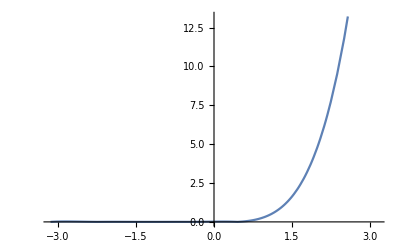

Найдем максимальную абсолютную величину разности между значениями функции и интерполяционного многочлена, вычисленного для значений xi между узлами интерполирования:

FindMaximum::fdssnv: Search specification π/7 without variables should be a list with 1 to 4 elements.

FindMaximum[{x Cos[x]-nwtn[x],-3.1415<x<3.1415},x]

0

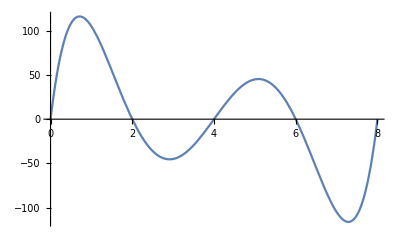

{-1.91183,{π/7→2.15584×10^-8}}

```mathematica
n =7;
a=-Pi;  b =Pi; h = (b-a)/n;

XDT = {}; YDT = {};
For[i=0,i≤n, i++,
xdata[i]=a+i*h;
ydata[i]=N[xdata[i]*Cos[xdata[i]]];
XDT=Append[XDT, xdata[i]];
YDT = Append[YDT, ydata[i]];
];
Array[xdata,{n+1,0}];
Array[ydata, {n+1,0}];
Print["n = ", n];
Print["Таблица данной функции:\n","XDT:   ", MatrixForm[XDT], "    YDT:   " MatrixForm[YDT]];



Print["Вычисляем таблицу разностей по рекуррентной формуле:"];
Array[diff, {n+1, n+1},{0,0}];
For[j=1,j≤n,j++,
For[i=n, i≥n-j,i--,diff[i,j]=""]];
For[i=0,i≤n,i++,diff[i,0]=ydata[i]];
For[j=1,j≤n,j++,
For[i=0,i≤n-j,i++,
diff[i,j]=(diff[i+1,j-1]-diff[i,j-1])/(xdata[i+j]-xdata[i])]];
tabl1=Array[diff,{n+1,n+1},{0,0}];

PaddedForm[TableForm[tabl1],{10,10}]



Print["Интреполяционные многочлены 1, 2, 3, 4 порядка:"]
plan = diff[0,0]+diff[0,1]*(x-xdata[0]);
n=4;list = List[plan];

For[i=2,i≤n,i++,
plan=list[[i-1]]+diff[0,i]*Product[(x-xdata[i]),{i,0,i-1}];
list=Append[list,plan]];
nwtn[x_]:=N[list[[n]]];

Column[list]
Column[Collect[list,x]]


Print["С помощью встроенной функции InterpolatingPolinomial получаем решение:"]

"Таблица данной функции:\n""XDT:   "({{-π}, {-(5 π)/7}, {-(3 π)/7}, {-π/7}, {π/7}, {(3 π)/7}, {(5 π)/7}, {π}})"    YDT:   " ({{3.141592653589793}, {1.399107843648252}, {-0.29960148488018434}, {-0.4043538823593361}, {0.4043538823593361}, {0.29960148488018434}, {-1.399107843648252}, {-3.141592653589793}})

data = {{-Pi,3.141592653589793},{-(5 π)/7,1.399107843648252},{-(3 π)/7,-0.29960148488018434},{-π/7,-0.4043538823593361},{π/7,0.4043538823593361},{(3 π)/7,0.29960148488018434}, {(5 π)/7,-1.399107843648252},{π,-3.141592653589793}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]

Print["Вывод графиков функции f(x),интерполяционного многочлена,также величины погрешности интерполирования на отрезке[-Pi,Pi]"]
Plot[{x*Cos[x],nwtn[x],Abs[x*Cos[x]-nwtn[x]]},{x,-Pi-1,Pi+1}, PlotLabels->"Expressions"]
Plot[{xdata[x]*Cos[xdata[x]],nwtn[x]},{x,-Pi-1,Pi+1}, PlotLabels->"Expressions"]




Pln={};
P[n+1] = 0;

For[i=n,i≥0,i--,P[i]=diff[0,i]+(x-xdata[i])*P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]





P[0]
nwtn[x_]:=P[0];m=40
XDAT={};YDAT={};nwtnDAT={};MR={};
For [i=0,i<=m,i++ ,
xdatas[i]=a+i*(h/10);
ydatas[i]=N[xdata[i]*Cos[xdata[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[x];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT,ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]] MatrixForm[YDAT] MatrixForm[nwtnDAT] MatrixForm[MR]

Print["Величина погрешности интерполирования(отдельно) на отрезке [-pi,pi]:"];
Plot[Abs[x*Cos[x]-nwtn[x]],{x,-Pi,Pi}]

Print["Найдем максимальную абсолютную величину разности между значениями функции и интерполяционного многочлена, вычисленного для значений xi между узлами интерполирования:"];
FindMaximum[{x*Cos[x]-nwtn[x], -3.1415 < x < 3.1415},x]

f[x_]:=Product[x-xdata[k],{k,0,n}]
Collect[f[x],x]


Plot[x^5-20*x^4+140*x^3-400*x^2+384*x,{x,0,8}]

FindMaximum[{f[x],0≤x≤8},{x,0}]
```